## Gaussian beam propagation

```mathematica
λ = 7.8*^-7; (*wavelength of laser [m]*)
```

#### Gaussian beam functions, ABCD matrices, etc

```mathematica
zR[w0_]:=(π  w0^2)/λ;(*Rayleigh range in vacuum [m]*)
w[z_,w0_]:= w0(1+(z/zR[w0])^2)^(1/2);(*beam waist [m]*)
RoC[z_,w0_]:= z(1+zR[w0]^2/z^2);(*RoC [m]*)
η[z_,w0_]:=ArcTan[z/zR[w0]];(*Guoy phase*)
q[z_,w0_]:=1/(1/RoC[z,w0]+(ⅈ λ)/(π w[z,w0]^2)); (*the mysterious q parameter*)
qM[q_,M_]:=(M[[1,1]]q+M[[1,2]])/(M[[2,1]]q+M[[2,2]]); (*q after an ABCD matrix M is applied*)
wq[q_,z_]:=√(λ/(π Im[1/(q+z)]));(*waist function*)
ThinLensM[f_]:={{1,0},{-1/f,1}};
FreeSpaceM[d_]:={{1,d},{0,1}};
(*This applies the transformations to the beam and plots the waist as a function of the optical axis*)
beamPropagate[qInit_,sys_,color_,legend_]:=Module[{q=qInit,qNext,plots={},i,element,z=0,zNext,x},
For[i=1,i≤Length[sys],i++,
element=sys[[i]];
qNext=qM[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[plots,Piecewise[{{wq[qNext,x-z]/10^-3,z<x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
]; (*waist in [m]*)
Plot[plots,{x,0,z},PlotRange->{0,All},Frame->False,PlotStyle->color]
]
```

#### Propagate and plot the beam

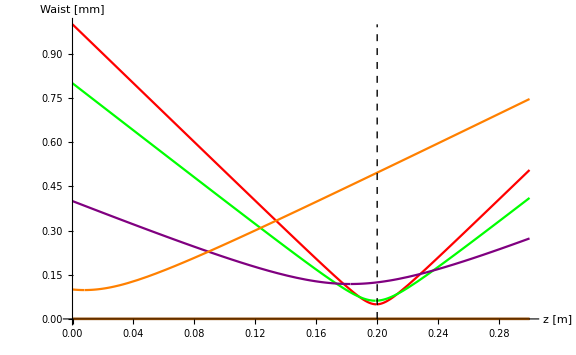

```mathematica
inputWaist = {0.001,0.0008,0.0004,0.0001}; (*system input waists wx,wy*)
colors = {Red,Green,Purple,Orange}; (*colors of waist plot lines*)
legends=Table[StringForm["``mm",waist/10^-3],{waist,inputWaist}];
d0 = .00; (*[m] distance beam travels to f1; arbitrary*)
d1 =0.1;
f1 = .2; (*[m] lens before EOM*)
lenses = {(*the system of optics*)
{FreeSpaceM[d0],d0},
{ThinLensM[f1],f1+d1}};
beamPlots ={};
For[i=1,i<Length[inputWaist]+1,i++,
q0 = Limit[q[b,inputWaist[[i]]],b->0];
AppendTo[beamPlots,beamPropagate[q0,lenses,colors[[i]],legends[[i]]]](*system input beam*)
]
Show[beamPlots,Graphics[{Dashed,Line[{{f1+d0,0},{f1+d0,Max[inputWaist]/10^-3}}]}],AxesLabel->{"z [m]","Waist [mm]"},ImageSize->Large,LabelStyle->Directive[Blue, Medium],PlotRange->All]
```

#### Fiber coupling

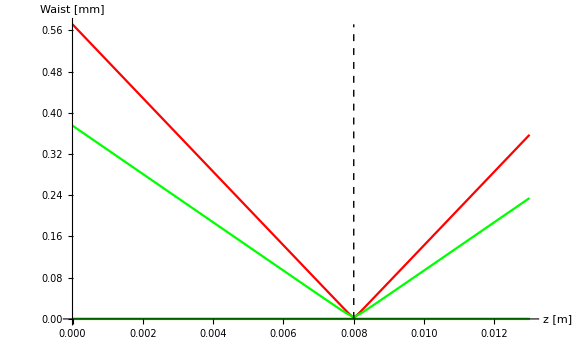

```mathematica
inputWaist = {0.001143/2,0.00075/2}; (*system input waists wx,wy*)
colors = {Red,Green}; (*colors of waist plot lines*)
legends=Table[StringForm["``mm",waist/10^-3],{waist,inputWaist}];
d0 = 0; (*[m] distance beam travels to f1; arbitrary*)
d1 =0.005;
f1 = .008; (*[m] coupling lens*)
lenses = {(*the system of optics*)
{FreeSpaceM[d0],d0},
{ThinLensM[f1],f1+d1}};
beamPlots ={};
For[i=1,i<Length[inputWaist]+1,i++,
q0 = Limit[q[b,inputWaist[[i]]],b->0];
AppendTo[beamPlots,beamPropagate[q0,lenses,colors[[i]],legends[[i]]]](*system input beam*)
]
Show[beamPlots,Graphics[{Dashed,Line[{{f1+d0,0},{f1+d0,Max[inputWaist]/10^-3}}]}],AxesLabel->{"z [m]","Waist [mm]"},ImageSize->Large,LabelStyle->Directive[Blue, Medium],PlotRange->All]
```